### encoder & decoder

#### images

```mathematica
enc=NetEncoder[{"Image",{128,128},"Grayscale"}]
```

NetEncoder[<>]

```mathematica
img = -Graphics-
code = enc@img
```

-Graphics-

{{1}}
 |  |  |  |

```mathematica
Dimensions@code
```

{1,128,128}

```mathematica
dec=NetDecoder[{"Image","Grayscale"}]
```

NetDecoder[<>]

```mathematica
dec@code
```

-Graphics-

#### classes

```mathematica
enc=NetEncoder[{"Class",{"male","female"}}]
```

NetEncoder[<>]

```mathematica
enc[{"male","female","female"}]
```

{1,2,2}

```mathematica
dec=NetDecoder[{"Class",{"male","female"}}]
```

NetDecoder[<>]

```mathematica
dec[{{.1,.9},{.6,.4}}]
```

{female,male}

#### characters

```mathematica
enc=NetEncoder["Characters"]
```

NetEncoder[<>]

```mathematica
cod=enc["what are you doing?"]
```

{90,75,68,87,3,68,85,72,3,92,82,88,3,71,82,76,81,74,34}

```mathematica
dec=NetDecoder[{"Characters"}]
```

NetDecoder[<>]

```mathematica
dat={UnitVector[97,90],UnitVector[97,75]}
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
dec[dat]
```

wh

#### tokens

#### sounds

```mathematica
enc=NetEncoder[{"Audio",SampleRate->16000}]
```

NetEncoder[<>]

```mathematica
aud=CloudGet[CloudObject["https://www.wolframcloud.com/obj/9623830f-efab-419f-a545-87038bfe9e32"]]
```

```mathematica
cod=enc@aud;
Short@cod
```

{{0.00129929},«29877»,{0.000768688}}

```mathematica
Audio[Flatten@cod,SampleRate->16000]
```

#### any function

```mathematica
enc=NetEncoder[{"Function",List@@ColorConvert[#,"Hue"]&,{3}}]
```

NetEncoder[<>]

```mathematica
dat=enc@RGBColor[1,0,0]
```

{0.,1.,1.}

```mathematica
dec=NetDecoder[{"Function",ColorConvert[Hue@Normal@#,"RGB"]&}]
```

NetDecoder[<>]

```mathematica
dec@dat
```

RGBColor[1., 0., 0.]

### FUNCTIONS, LAYERS, CHAINSandGRAPHS

#### functions

```mathematica
MyAdd[x_]:=x+3
```

```mathematica
MyAdd[3]
```

6

```mathematica
?MyAdd
```

```mathematica
MyAdd[x_,y_]:=x+y
```

```mathematica
MyAdd/@{3,4,5}
```

{6,7,8}

```mathematica
myAdd:=#+3&
```

#### functions as layers

```mathematica
lay=ElementwiseLayer[#+.2&]
```

```mathematica
lay[4]
```

4.2

```mathematica
lay[{{2,3,4},{2,3,4},{2,3,4}}]
```

{{2.2,3.2,4.2},{2.2,3.2,4.2},{2.2,3.2,4.2}}

#### single layer network

```mathematica
enc=NetEncoder[{"Image",{32,32},"RGB"}]
```

NetEncoder[<>]

```mathematica
dec=NetDecoder[{"Image"}]
```

NetDecoder[<>]

```mathematica
img=CloudGet@CloudObject["https://www.wolframcloud.com/obj/ce4ebe09-1d86-4c71-ad74-a3e12090822b"]
```

-Graphics-

```mathematica
cod=enc@img;
Dimensions@cod
```

{3,32,32}

```mathematica
dec@enc@img
```

-Graphics-

```mathematica
dec@lay@enc@img
```

-Graphics-

```mathematica
net=NetChain[{lay},"Input"->enc,"Output"->dec]
```

NetChain[<>]

```mathematica
net@img
```

-Graphics-

```mathematica
net=NetChain[{ElementwiseLayer[#+.2&],TransposeLayer[TwoWayRule[2,3]]},"Input"->NetEncoder[{"Image",{48,32},"RGB"}],"Output"->NetDecoder[{"Image"}]]
```

NetChain[<>]

```mathematica
net@img
```

-Graphics-

#### network as a GRAPH of layers

```mathematica
net=NetGraph[{ElementwiseLayer[#+.2&],TransposeLayer[TwoWayRule[2,3]]},{NetPort["Input"]->1->2->NetPort["Output"]},"Input"->NetEncoder[{"Image",{48,32},"RGB"}],"Output"->NetDecoder[{"Image"}]]
```

NetGraph[<>]

```mathematica
net@img
```

-Graphics-

### train network

```mathematica
net=NetInitialize@NetGraph[{NetArrayLayer["Array"->{.5}],ThreadingLayer[Plus]},{1->2->NetPort["Output"],NetPort["Input"]->2},"Input"->{1},"Output"->{1}]
```

NetGraph[<>]

```mathematica
NetExtract[net,{1,"Arrays"}][[1]]//Normal
```

{0.5}

```mathematica
net[2]
```

{2.5}

```mathematica
net[{{2},{3},{1.4}}]
```

{{2.5},{3.5},{1.9}}

```mathematica
samples={{1}->{1.1},{2}->{2.1},{1.6}->{1.7}};
```

```mathematica
net1=NetTrain[net,samples]
```

NetGraph[<>]

```mathematica
Normal@NetExtract[net1,{1,"Arrays"}][[1]]
```

{0.1}

```mathematica
net1@3
```

{3.1}

### BACKPROPAGATION

#### 1 D

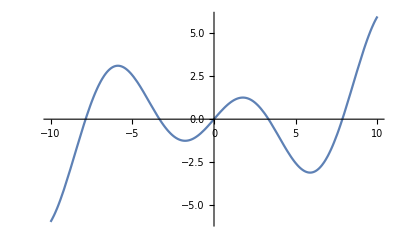

```mathematica
func[x_]:=Sin[.4 x]+.7Cos[.6 x] x;
Plot[func[x],{x,-10,10}]
```

```mathematica
NMinimize[{func[x],-7<x<7},{x},Method->"DifferentialEvolution"]
```

{-3.10246,{x→5.87958}}

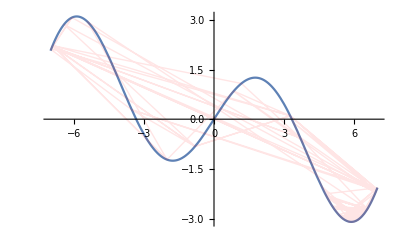

```mathematica
{sol,trace}=Reap[NMinimize[{func[x],-7<x<7},{x},Method->"DifferentialEvolution",EvaluationMonitor:>Sow[x]]];
Show[Plot[func[x],{x,-7,7}],Graphics[{Red,Opacity@.1,Line@Cases[First[trace],x_:>{x,func@x},1]}]]
```

```mathematica
pts=Cases[First[trace],x_:>{x,func@x},1];
Manipulate[Show[Plot[func[x],{x,-7,7}],Graphics[{Red,PointSize@.02,Point@pts[[n]]}]],{{n,1},1,Length@pts,1}]
```

#### 2 D

```mathematica
func[x_,y_]:=x^4-2x^2+y^4-2y^2+.1 x+.2 y;
{sol3D,trace3D}=Reap[NMinimize[{func[x,y],-1.3<x<1.3&&-1.3<y<1.3},{x,y},Method->"DifferentialEvolution",EvaluationMonitor:>Sow[{x,y}]]];
sol3D
pts3D=Cases[trace3D,{x_,y_}:>{x,y,func[x,y]},All];
Manipulate[Show[Plot3D[func[x,y],{x,-1.3,1.3},{y,-1.3,1.3},PlotRange->{-2.5,0.1},AspectRatio->1,PlotStyle->Directive[Opacity[0.2]]],Graphics3D[{Red,Sphere[pts3D[[n]],.05]}]],{{n,1},1,Length@pts3D,1}]
```

{-2.30306,{x→-1.01227,y→-1.02412}}

#### the fully connected LINEAR LAYER

```mathematica
linear=NetInitialize@LinearLayer[2,"Input"->3]
```

LinearLayer[<>]

```mathematica
weights=Normal@NetExtract[linear,"Arrays"]["Weights"]
```

{{0.0132589,0.613868,0.238377},{0.353536,0.3161,-0.996597}}

```mathematica
biases=Normal@NetExtract[linear,"Arrays"]["Biases"]
```

{0.,0.}